The following code adds up cost when do backtesting by Liu Hua-shan

```mathematica
JLHold[stkPrice_]:=Module[{capitals,position,ttassets,trdprice,svramout,taxamout,capitals2,position2,ttassets2,trdprice2,svramout2,taxamout2,buyHands,result},
capitals=Last[tradeList][[1]];
position=Last[tradeList][[2]];
ttassets=Last[tradeList][[3]];
trdprice=Last[tradeList][[4]];
svramout=Last[tradeList][[5]];
taxamout=Last[tradeList][[6]];
(*not buy*)
capitals2=capitals;
position2=position;
ttassets2=capitals+position*stkPrice;
trdprice2=stkPrice;
svramout2=0;
taxamout2=0;
tradeList=AppendTo[tradeList,Round[#,0.01]&@{capitals2,position2,ttassets2,trdprice2,svramout2,taxamout2}];
(*return result*)
Return[Flatten@{"Hold:",Last@tradeList}];
]

JLBuy[buyRate_,buyPrice_,svrRate_,taxRate_]:=Module[{capitals,position,ttassets,trdprice,svramout,taxamout,capitals2,position2,ttassets2,trdprice2,svramout2,taxamout2,buyHands,result},
capitals=Last[tradeList][[1]];
position=Last[tradeList][[2]];
ttassets=Last[tradeList][[3]];
trdprice=Last[tradeList][[4]];
svramout=Last[tradeList][[5]];
taxamout=Last[tradeList][[6]];

(*do buy*)
buyHands=Floor[capitals*buyRate/(buyPrice*100(1+svrRate+taxRate))];
If[buyHands>0,
(*do buy*)
capitals2=capitals-buyHands*buyPrice*100(1+taxRate)-Max[buyHands*buyPrice*100*svrRate,5];
position2=position+buyHands*100;
ttassets2=capitals2+position2*buyPrice;
trdprice2=buyPrice;
svramout2=Max[buyHands*buyPrice*100*svrRate,5.00];
taxamout2=buyHands*buyPrice*100*taxRate;
tradeList=AppendTo[tradeList,Round[#,0.01]&@{capitals2,position2,ttassets2,trdprice2,svramout2,taxamout2}],
(*not buy*)
JLHold[buyPrice];
];
(*return result*)
Return[Flatten@{"Buy:",Last@tradeList}];
]

JLSell[sellRate_,sellPrice_,svrRate_,taxRate_]:=Module[{capitals,position,ttassets,trdprice,svramout,taxamout,capitals2,position2,ttassets2,trdprice2,svramout2,taxamout2,sellHands,sellQuans,result},
capitals=Last[tradeList][[1]];
position=Last[tradeList][[2]];
ttassets=Last[tradeList][[3]];
trdprice=Last[tradeList][[4]];
svramout=Last[tradeList][[5]];
taxamout=Last[tradeList][[6]];

(*check availabe*)
sellHands=Floor[position*sellRate/100];
sellQuans =If[sellHands>1,sellHands*100,position];

If[position>0,
(*do sell*)
capitals2=capitals+sellQuans*sellPrice(1-taxRate)-Max[sellQuans*sellPrice*svrRate,5];
position2=position-sellQuans;
ttassets2=capitals2+position2*sellPrice;
trdprice2=sellPrice;
svramout2=Max[sellQuans*sellPrice*svrRate,5];
taxamout2=sellQuans*sellPrice*taxRate;
tradeList=AppendTo[tradeList,Round[#,0.01]&@{capitals2,position2,ttassets2,trdprice2,svramout2,taxamout2}],
(*not sell*)
JLHold[sellPrice]];
(*return result*)
Return[Flatten@{"Sell:",Last@tradeList}];
]

BacktestDo[list_List,buyRate_,sellRate_,svrRate_,taxRate_]:=
If[Last@list<=0,
JLBuy[buyRate,First[list],svrRate,0],
JLSell[sellRate,First[list],svrRate,taxRate]]
```

```mathematica
lstPrice={{4.66,-0.05},{4.69,0.03},{4.78,0.09},{4.78,0.},{4.81,0.03},{4.85,0.04},{4.78,-0.07},{5.1,0.32},{5.29,0.19},{5.19,-0.1},{5.28,0.09},{5.22,-0.06},{5.18,-0.04},{5.07,-0.11},{5.08,0.01},{5.09,0.01},{5.07,-0.02},{5.1,0.03},{5.05,-0.05},{5.05,0.},{5.13,0.08},{5.1,-0.03},{5.09,-0.01},{5.21,0.12},{5.24,0.03},{5.26,0.02},{5.35,0.09},{5.19,-0.16},{5.24,0.05},{5.09,-0.15},{5.18,0.09},{5.19,0.01},{5.18,-0.01},{5.13,-0.05},{5.15,0.02},{5.06,-0.09},{5.09,0.03},{5.08,-0.01},{5.01,-0.07},{4.99,-0.02},{4.99,0.},{4.94,-0.05},{4.98,0.04},{4.92,-0.06},{4.87,-0.05},{4.91,0.04},{4.91,0.},{4.92,0.01},{4.95,0.03},{4.9,-0.05},{4.93,0.03},{4.99,0.06},{5.04,0.05},{4.98,-0.06},{5.17,0.19},{5.07,-0.1},{5.08,0.01},{5.14,0.06},{5.17,0.03},{5.07,-0.1}};
```

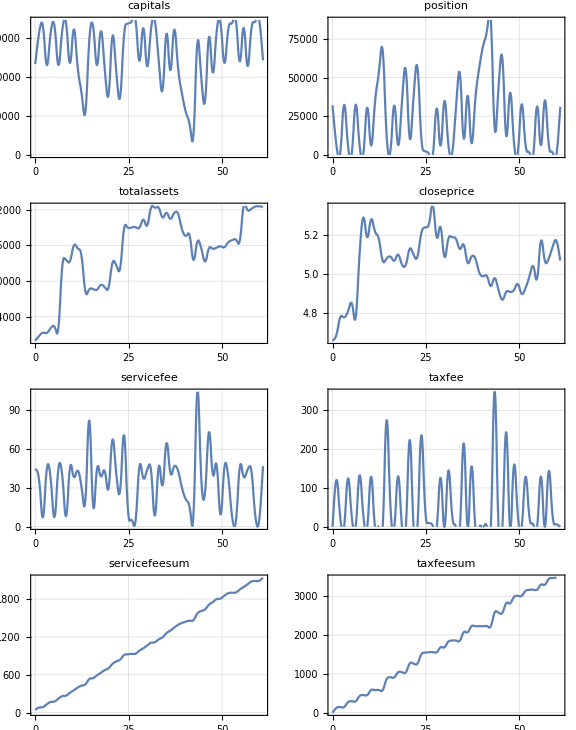

```mathematica
tradeList={{500000,0,500000,0,0,0}};
buyRate=0.3;
sellRate=0.8;
svrRate=0.0003;
taxRate=0.001;
BacktestDo[#,buyRate,sellRate,svrRate,taxRate]&/@lstPrice;
tradeList=Rest@tradeList;
{capitals,position,totalassets,closeprice,servicefee,taxfee}=Table[tradeList[[All,i]],{i,1,6}];
servicefeesum=Accumulate[servicefee];
taxfeesum=Accumulate[taxfee];

GraphicsGrid[Partition[#,2]&@Map[ListLinePlot[ToExpression[#],DataRange->Length[lstPrice]+1,PlotLabel->#,ImagePadding->{{40,10},{Automatic,Automatic}},PlotRange->All,InterpolationOrder->2,
Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray, Dotted]]&,
{"capitals","position","totalassets","closeprice","servicefee","taxfee","servicefeesum","taxfeesum"}],ImageSize->Large]
```